```mathematica
SetDirectory[NotebookDirectory[]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Functions

```mathematica
R=20000;
Mc=1.4691897661033038;
Mb=4.882;
kfinal={0.6856700331366409,-0.31661256911352553};(*100k run*)
kfinalu={0.9065399936425322,-0.36858869824209667};
kfinall={0.4648000726307495,-0.2646364399849544};
αcont={0.5129548374487685,0.002435119807500435};(*10k run*)
σcont={0.16999653850906107,0.000838106749908169};
ccont={-0.1611740456186636,0.002474788649682089};
conv=0.197327;
ReVsbVac=8/10;
Tlim=1584/10000;
w=0.66;
Jpsimass=3.0969;
Psi2smass=3.6632;
```

```mathematica
v[ϕ_,pT_,Jpsi_,Psi2s_]:=√(1-((1-w^2)(Jpsi Jpsimass + Psi2s Psi2smass)^2)/((Jpsi Jpsimass + Psi2s Psi2smass)^2-2 √((Jpsi Jpsimass + Psi2s Psi2smass)^2+pT^2)w pT Cos[ϕ]+w^2 pT^2 Cos[ϕ]^2+pT^2));
```

### Self energies

```mathematica
mDcalmu[T_,μ_,c_,d_]:=SetPrecision[Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ],30];
```

```mathematica
Πpar[θ_,mD_,u_]:=SetPrecision[mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))]),30];
```

### IIT paper

#### Potentials

```mathematica
ReVcpp[r_,mD_,u_,α_,c_]:=Re[c-α/r+α  NIntegrate[Sin[θ] √Πpar[θ,mD,u] Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*INCORRECT*)
ReVspp[r_,mD_,u_,σ_]:=Re[σ NIntegrate[Sin[θ] 1/(√Πpar[θ,mD,u])Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*INCORRECT*)
ReVsp[r_,mD_,u_,σ_]:=σ NIntegrate[Sin[θ] 1/Re[√Πpar[θ,mD,u]] Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];(*OUR MODEL DIFFERS HERE*)
ReVcp[r_,mD_,u_,α_,c_]:=c-α mD-α/r+α NIntegrate[Sin[θ]Re[√Πpar[θ,mD,u]]Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];(*WE USE THIS ONE*)
```

```mathematica
ImVcp[r_,mD_,u_,α_,T_]:=2 α T Quiet[NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,mD,u]-Conjugate[Πpar[x,mD,u]])(Sinh[√Πpar[x,mD,u] r Cos[x]]SinhIntegral[√Πpar[x,mD,u] r Cos[x]]-Cosh[√Πpar[x,mD,u] r Cos[x]]CoshIntegral[√Πpar[x,mD,u] r Cos[x]]-Sinh[√Conjugate[Πpar[x,mD,u]] r Cos[x]]SinhIntegral[√Conjugate[Πpar[x,mD,u]] r Cos[x]]+Cosh[√Conjugate[Πpar[x,mD,u]] r Cos[x]]CoshIntegral[√Conjugate[Πpar[x,mD,u]] r Cos[x]]),{x,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*WE USE THIS ONE*)
```

#### Permittivities

```mathematica
ϵRepp[r_,mD_,u_]:=Re[1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Πpar[θ,mD,u]Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ] Πpar[θ,mD,u]^(3/2)Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2}])];(*INCORRECT*)
ϵRep[r_,mD_,u_]:=1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,mD,u]]Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ]Re[Πpar[θ,mD,u]^(3/2)]Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2}]);(*OLD*)
```

```mathematica
ϵImp[r_,mD_,u_,T_]:=
1/(2π)Re[T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,mD,u]-Conjugate[Πpar[x,mD,u]])1/r Cos[x] (2 √Conjugate[Πpar[x,mD,u]] (CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]] Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+r Conjugate[Πpar[x,mD,u]] Cos[x] (Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+√Πpar[x,mD,u] (-CoshIntegral[r Cos[x] √Πpar[x,mD,u]] (r Cos[x] Cosh[r Cos[x] √Πpar[x,mD,u]] √Πpar[x,mD,u]+2 Sinh[r Cos[x] √Πpar[x,mD,u]])+(2 Cosh[r Cos[x] √Πpar[x,mD,u]]+r Cos[x] √Πpar[x,mD,u] Sinh[r Cos[x] √Πpar[x,mD,u]]) SinhIntegral[r Cos[x] √Πpar[x,mD,u]])),{x,0,π/2},WorkingPrecision->20]];(*UNREGULATED*)
```

```mathematica
D[Sin[θ]f[θ,mD,u]Exp[-f[θ,mD,u]r Cos[θ]],{r,2}]+2/r D[Sin[θ]f[θ,mD,u]Exp[-f[θ,mD,u]r Cos[θ]],r]//FullSimplify
```

(ⅇ^(-r Cos[θ] f[θ,mD,u]) Cos[θ] f[θ,mD,u]^2 (-2+r Cos[θ] f[θ,mD,u]) Sin[θ])/r

```mathematica
ϵRep1[r_,mD_,u_]:=Quiet[NIntegrate[(ⅇ^(-r Cos[θ] Re[√Πpar[θ,mD,u]]) Cos[θ] Re[√Πpar[θ,mD,u]]^2 (-2+r Cos[θ] Re[√Πpar[θ,mD,u]]) Sin[θ])/r,{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*WE USE THIS ONE*)
```

### Tabs

```mathematica
ReVsTab[mD1_,u1_,σ1_]:=Block[{u=u1,mD=mD1,σ=σ1,inter0,inter1,tab,inter2,inter3,tab1,tab0},tab0=ParallelTable[{r,σ r^2 ϵRep1[r,mD,u]},{r,10^-10,100,1/20}];
inter0=Interpolation[tab0];
inter1[r_]:=Quiet[NIntegrate[inter0[r1],{r1,0,r}]];
tab=ParallelTable[{r,inter1[r]+σ},{r,0,100,1/20}];
inter2=Interpolation[tab];
inter3[r_]:=Quiet[NIntegrate[inter2[r1],{r1,0,r}]];
tab1=ParallelTable[{r,inter3[r]},{r,0,100,1/20}];
Return[tab1]];
```

```mathematica
reg=303689/100000;
```

```mathematica
ImVsTab[mD1_,u1_,σ1_,T1_]:=Block[{u=u1,mD=mD1,σ=σ1,T=T1,tab0,tab1,inter0,inter1,inter2,temp,tab2},tab0=Table[{r,4π σ r^2 ϵImp[r,mD,u,T]},{r,10^-10,100,1/20}];
inter0=Interpolation[tab0];
inter1[r_]:=Quiet[NIntegrate[inter0[r1],{r1,10^-10,r}]];
temp=inter1[10^-10];
tab1=ParallelTable[{r,inter1[r]-temp},{r,10^-10,100,1/20}];
inter1=Interpolation[tab1];
inter2[r_]:=Quiet[NIntegrate[inter1[r1],{r1,10^-10,r}]];
tab2=ParallelTable[{r,inter2[r]},{r,10^-10,100,1/20}];
Return[tab2]];
```

### Make potentials for pT=0

```mathematica
Export["pots/par/ReVspT0.dat",ReVsTab[mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],w,σcont[[1]]]];//AbsoluteTiming
```

{536.712,Null}

```mathematica
Export["pots/par/ImVspT0.dat",ImVsTab[SetPrecision[mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],30],SetPrecision[w,30],SetPrecision[σcont[[1]],30],Tlim]];//AbsoluteTiming
```

{2331.57,Null}

```mathematica
Block[{temp,temp1},temp=ImVcp[10^-10,SetPrecision[mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],30],SetPrecision[w,30],SetPrecision[αcont[[1]],30],Tlim];temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],30],SetPrecision[w,30],SetPrecision[αcont[[1]],30],Tlim]-temp},{r,1/1000,100,1/20}];
Export["pots/par/ImVcpT0.dat",temp1];]//AbsoluteTiming
```

{795.082,Null}

```mathematica
Block[{temp},temp=Join[ParallelTable[{r,ReVcp[r,mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],w,αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/20}],{{500,ReVcp[500,mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],w,αcont[[1]],ccont[[1]]]}}];Export["pots/par/ReVcpT0.dat",temp];]//AbsoluteTiming
```

{35.9928,Null}

### Make potentials for pT=/=0

```mathematica
ang=Table[i,{i,0,π,π/50}]
```

{0,π/50,π/25,(3 π)/50,(2 π)/25,π/10,(3 π)/25,(7 π)/50,(4 π)/25,(9 π)/50,π/5,(11 π)/50,(6 π)/25,(13 π)/50,(7 π)/25,(3 π)/10,(8 π)/25,(17 π)/50,(9 π)/25,(19 π)/50,(2 π)/5,(21 π)/50,(11 π)/25,(23 π)/50,(12 π)/25,π/2,(13 π)/25,(27 π)/50,(14 π)/25,(29 π)/50,(3 π)/5,(31 π)/50,(16 π)/25,(33 π)/50,(17 π)/25,(7 π)/10,(18 π)/25,(37 π)/50,(19 π)/25,(39 π)/50,(4 π)/5,(41 π)/50,(21 π)/25,(43 π)/50,(22 π)/25,(9 π)/10,(23 π)/25,(47 π)/50,(24 π)/25,(49 π)/50,π}

```mathematica
pT=25;
```

```mathematica
Do[Export["pots/par/pT25/ReVspT"<>ToString[pT]<>"ang"<>ToString[i]<>"Jpsi.dat",ReVsTab[mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],v[ang[[i]],pT,1,0],σcont[[1]]]],{i,1,Length[ang]}];//AbsoluteTiming
```

```mathematica
Do[Export["pots/par/pT25/ImVspT"<>ToString[pT]<>"ang"<>ToString[i]<>"Jpsi.dat",ImVsTab[SetPrecision[mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],30],SetPrecision[v[ang[[i]],pT,1,0],30],SetPrecision[σcont[[1]],30],Tlim]],{i,39,Length[ang]}];//AbsoluteTiming
```

```mathematica
Block[{temp,temp1},Do[temp=ImVcp[10^-10,SetPrecision[mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],30],SetPrecision[v[ang[[i]],pT,1,0],30],SetPrecision[αcont[[1]],30],Tlim];temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],30],SetPrecision[v[ang[[i]],pT,1,0],30],SetPrecision[αcont[[1]],30],Tlim]-temp},{r,1/1000,100,1/20}];
Export["pots/par/pT25/ImVcpT"<>ToString[pT]<>"ang"<>ToString[i]<>"Jpsi.dat",temp1];,{i,1,Length[ang]}]]//AbsoluteTiming
```

```mathematica
Block[{temp},Do[temp=Join[ParallelTable[{r,ReVcp[r,mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],v[ang[[i]],pT,1,0],αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/20}],{{500,ReVcp[500,mDcalmu[Tlim,0,kfinal[[1]],kfinal[[2]]],v[ang[[i]],pT,1,0],αcont[[1]],ccont[[1]]]}}];Export["pots/par/pT25/ReVcpT"<>ToString[pT]<>"ang"<>ToString[i]<>"Jpsi.dat",temp];,{i,1,Length[ang]}]]//AbsoluteTiming
```

{35.9928,Null}

## Spectra

### pT = 0

```mathematica
Block[{data},data=ToExpression[Import["pots/par/pT0/ReVspT0Jpsi.dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVs=Interpolation[data,InterpolationOrder->1]];
```

```mathematica
Block[{data},data=ToExpression[Import["pots/par/pT0/ReVcpT0Jpsi.dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVc=Interpolation[data,InterpolationOrder->1]];
```

```mathematica
Block[{data},data=ToExpression[Import["pots/par/pT0/ImVspT0Jpsi.dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVs=Interpolation[data,InterpolationOrder->1]];
```

```mathematica
Block[{data},data=ToExpression[Import["pots/par/pT0/ImVcpT0Jpsi.dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVc=Interpolation[data,InterpolationOrder->1]];
```

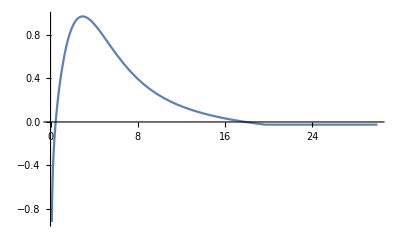

```mathematica
Plot[ReVs[r/0.197]+ReVc[r/0.197],{r,0,30}]
```

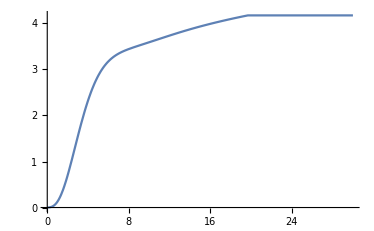

```mathematica
Plot[ImVc[r/0.197]+ImVs[r/0.197],{r,0,30}]
```

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

```mathematica
pT=0;
```

```mathematica
swaveccspectra[ang_]:=Block[{α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVs[r]+ReVc[r]+ⅈ(ImVs[r]+ImVc[r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc/par/pT"<>ToString[pT]<>"/swccpT"<>ToString[pT]<>"spectraJpsi.dat",Sort[ccss]];
];
```

```mathematica
swaveccspectra[0]
```

### pT =/= 0

#### Funcs

```mathematica
PotsIn[pT1_]:=Block[{pT=pT1},
ReVs=ConstantArray[0,51];
ReVc=ConstantArray[0,51];
ImVc=ConstantArray[0,51];
ImVs=ConstantArray[0,51];
Do[Block[{data},data=ToExpression[Import["pots/par/pT"<>ToString[pT]<>"/ReVspT"<>ToString[pT]<>"ang"<>ToString[i]<>"Jpsi.dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVs[[i]]=Interpolation[data,InterpolationOrder->1]];,{i,1,51}]
Do[Block[{data},data=ToExpression[Import["pots/par/pT"<>ToString[pT]<>"/ReVcpT"<>ToString[pT]<>"ang"<>ToString[i]<>"Jpsi.dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVc[[i]]=Interpolation[data,InterpolationOrder->1]];,{i,1,51}]
Do[Block[{data},data=ToExpression[Import["pots/par/pT"<>ToString[pT]<>"/ImVspT"<>ToString[pT]<>"ang"<>ToString[i]<>"Jpsi.dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVs[[i]]=Interpolation[data,InterpolationOrder->1]];,{i,1,51}]
Do[Block[{data},data=ToExpression[Import["pots/par/pT"<>ToString[pT]<>"/ImVcpT"<>ToString[pT]<>"ang"<>ToString[i]<>"Jpsi.dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVc[[i]]=Interpolation[data,InterpolationOrder->1]];,{i,1,51}];]
```

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

```mathematica
swaveccspectra[ang_]:=Block[{α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVs[[ang]][r]+ReVc[[ang]][r]+ⅈ(ImVs[[ang]][r]+ImVc[[ang]][r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc/par/pT"<>ToString[pT]<>"/swccpT"<>ToString[pT]<>"ang"<>ToString[ang]<>"spectraJpsi.dat",Sort[ccss]];
];
```

#### Run

```mathematica
pT=10;
PotsIn[pT]
Do[swaveccspectra[i],{i,15,51}]
```

```mathematica
pT=15;
PotsIn[pT]
Do[swaveccspectra[i],{i,1,51}]
```

## Fitting

### Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;
fit[input_,output_,scan_]:=Module[{temp=Range[1,scan],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,scan}];output=temp;];

fitONE[input_,output_]:=Module[{temp,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
maxx=Max[input[[All,1]]];
minx=Min[input[[All,1]]];
maxy=Max[input[[All,2]]];
maxyx=input[[Position[input,Max[input[[All,2]]]][[1,1]],1]];
maxyi=Position[input[[All,1]],maxyx][[1,1]];
maxxy=input[[Position[input,Max[input[[All,1]]]][[1,1]],2]];
inter=Interpolation[input,InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[[All,1]],Nearest[input[[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[[maxxis[[i]]-30,2]]>input[[maxxis[[i]],2]],input[[maxxis[[i]]+30,2]]>input[[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[[All,2]],Min[input[[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input]]];,
hwhmi=Position[input,Nearest[input[[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input],maxyi+3(maxyi-hwhmi),Length[input]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input,Nearest[input[[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp=Range[Length[hwhmi]];
Do[temp[[i]]=NonlinearModelFit[inputc[[i]],{BW[x,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},x,MaxIterations->1000],{i,Length[hwhmi]}];output=temp;]

store[param_,res_,model_,pT_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=param/.model[[i]]["BestFitParameters"],{i,Length[res]}];Export["results/par/pT"ToString[pT]<>temp<>".dat",res];];

storearea[res_,model_,pT_]:=Module[{temp=ToString[res]},res=Range[Length[model]];Do[res[[i]]=π/2(Γ/.model[[i]]["BestFitParameters"])( const/.model[[i]]["BestFitParameters"]),{i,Length[res]}];Export["results/par/pT"<>ToString[pT]<>temp".dat",res];];

import[res_,pT_]:=res=Import["results/par/pT"<>ToString[pT]<>ToString[res]<>".dat"];
```

### Perform fitting

```mathematica
pT=2;
```

```mathematica
Do[ccdata[i]=Import["cc/par/pT"<>ToString[pT]<>"/swccpT"<>ToString[pT]<>"ang"<>ToString[i]<>"spectraJpsi.dat"];,{i,51}];
```

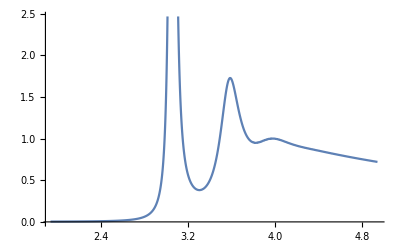

```mathematica
Block[{i=1},ListPlot[ccdata[i],Joined->True]]
```

```mathematica
Clear[ccmodel]
fit[ccdata,ccmodel,51];
```

$Aborted

```mathematica
Clear[wrfitcc,gfitcc,areafitcc,cfitcc,dfitcc,sfitcc,s2fitcc];
```

```mathematica
store[wr,wrfitcc,ccmodel];
store[Γ,gfitcc,ccmodel];
store[const,cfitcc,ccmodel];
store[δbg,dfitcc,ccmodel];
store[shift,sfitcc,ccmodel];
store[shift2,s2fitcc,ccmodel];
storearea[areafitcc,ccmodel];
```

### Import previous results

```mathematica
import[wrfitcc];
import[gfitcc];
import[cfitcc];
import[dfitcc];
import[sfitcc];
import[s2fitcc];
import[areafitcc];
```

### View results

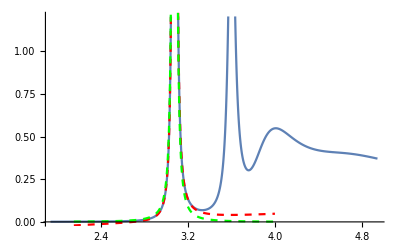

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```